```mathematica
SetOptions[{ListPlot3D,Histogram,Plot},ImageSize->Small];
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
SetDirectory["C:\\Users\\PC\\Pictures\\Lab4_Supplementary"]
```

C:\Users\PC\Pictures\Lab4_Supplementary

```mathematica
T0:=Import["val_2022.png"]
```

```mathematica
ImageDimensions[T0]
```

{101,102}

```mathematica
ImageChannels[T0]
```

3

```mathematica
T1=RemoveAlphaChannel[T0]
```

-Graphics-

```mathematica
{TG=ColorConvert[T1,"Grayscale"]}
```

{-Graphics-}

```mathematica
{CRed,CGreen,CBlue}=ColorSeparate[T1]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{T3=ColorCombine[{CGreen,CRed,CBlue}]}
```

{-Graphics-}

```mathematica
M3 = ImageData[CRed];
```

```mathematica
ListPlot3D[M3,ImageSize->Small]
```

-Graphics3D-

```mathematica
{M3Image=Image[M3]}
```

{-Graphics-}

```mathematica
C1:=Import["baboon.jpg"]
```

```mathematica
{C1Red,C1Green,C1Blue}=ColorSeparate[C1]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{C1Red}
```

{-Graphics-}

```mathematica
{C1Green}
```

{-Graphics-}

```mathematica
{C1Blue}
```

{-Graphics-}

```mathematica
{C1new=ColorCombine[{C1Green,C1Red,C1Blue}],C1}
```

{-Graphics-,-Graphics-}

```mathematica
{T5=Import["textold.jpg"]}
```

{-Graphics-}

```mathematica
ImageDimensions[T5]
```

{332,254}

```mathematica
T5GL:=ColorConvert[T5,"Grayscale"]
```

```mathematica
{T5GL}
```

{-Graphics-}

```mathematica
T5B:=Binarize[T5GL,0.2];
```

```mathematica
{T5B}
```

{-Graphics-}

```mathematica
{Dynamic[Binarize[T5GL,Tre]]}
```

{}

```mathematica
{Slider[Dynamic[Tre],Background->LightBlue],Dynamic[Tre]}
```

{,}

```mathematica
Tre6=FindThreshold[T5GL]
```

0.301961

```mathematica
T6:=Binarize[T5GL,Tre6]
```

```mathematica
{T6}
```

{-Graphics-}

```mathematica
R1:=Import["river1.JPG"]
```

```mathematica
{R1}
```

{-Graphics-}

```mathematica
R2=ColorConvert[R1,"Grayscale"];
```

```mathematica
{R2}
```

{-Graphics-}

```mathematica
R3=ColorNegate[R2];
```

```mathematica
{R3}
```

{-Graphics-}

```mathematica
{Dynamic[Binarize[R3,Tr3]]}
```

{}

```mathematica
{Slider[Dynamic[Tr3],Background->LightBlue],Dynamic[Tr3]}
```

{,}

```mathematica
{Slider[,Background->RGBColor[0.7000000000000001, 0.92, 0.74]],}
```

{Slider[,Background→RGBColor[0.7000000000000001, 0.92, 0.74]],}

```mathematica
{R4:=Binarize[R3,0.222]}
```

{Null}

```mathematica
{R4}
```

{-Graphics-}

```mathematica
RF3=Flatten[ImageData[R3]];
```

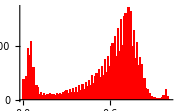

```mathematica
HP=Histogram[RF3,{0.01},ChartStyle->Red]
```

```mathematica
{Slider[Dynamic[TreP],Background->LightBlue],Dynamic[TreP]}
```

{,}

```mathematica
Dynamic[Show[HP,ListPlot[{{TreP,0}},PlotStyle->PointSize[0.06]]]]
```

```mathematica
{RH4=Dynamic[Binarize[R3,TreP]]}
```

{}

```mathematica
HL1=Import["Heavy_load_noisy.jpg"]
```

-Graphics-

```mathematica
ImageChannels[HL1]
```

3

```mathematica
HL2=ColorConvert[HL1,"Grayscale"]
```

-Graphics-

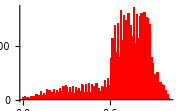

```mathematica
HHL=Histogram[Flatten[ImageData[HL2]],100,ChartStyle->Red]
```

```mathematica
{Slider[Dynamic[TreHL],Background->LightBlue],Dynamic[TreHL]}
```

{,}

```mathematica
Dynamic[Show[HHL,ListPlot[{{TreHL,0}},PlotStyle->PointSize[0.03]]]]
```

```mathematica
HL3=Dynamic[Binarize[HL2,TreHL]]
```

```mathematica
T12:=-Graphics-
```

```mathematica
{T9=ColorConvert[T12,"Grayscale"]}
```

{-Graphics-}

```mathematica
T9F:=Flatten[ImageData[T9]]
```

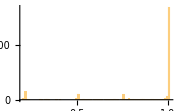

```mathematica
HP9=Histogram[T9F,{0.01}]
```

```mathematica
{T91=Binarize[T9,{0.1,0.3}]}
```

{-Graphics-}

```mathematica
{T92=Binarize[T9,{0.4,0.6}]}
```

{-Graphics-}

```mathematica
{T93=Binarize[T9,{0.7,0.8}]}
```

{-Graphics-}

```mathematica
{Tdown = ImageMultiply[T5, 0.5]}
```

{-Graphics-}

```mathematica
{Tup=ImageMultiply[T5,1.5]}
```

{-Graphics-}

```mathematica
Mona:=Import["mona.jpg"]
```

```mathematica
{MonaR,MonaG,MonaB}=ColorSeparate[Mona]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{MonaBnew=ImageMultiply[MonaB,1.5]}
```

{-Graphics-}

```mathematica
{MonaNew=ColorCombine[{MonaR,MonaG,MonaBnew}]}
```

{-Graphics-}

```mathematica
{Mona,MonaNew}
```

{-Graphics-,-Graphics-}

```mathematica
a:=0.8
```

```mathematica
f1[x_]:=1 / 2 (1+1 / Tan[a*Pi / 2]*Tan[a Pi (x-1 /2)])
```

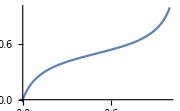

```mathematica
Plot[f1[x],{x,0,1}]
```

```mathematica
{MonaNew1=ImageApply[f1,Mona]}
```

{-Graphics-}

```mathematica
{Mona,MonaNew1}
```

{-Graphics-,-Graphics-}

```mathematica
MonaG:=ColorConvert[Mona,"Grayscale"]
```

```mathematica
MonaGNew1:=ColorConvert[MonaNew1,"Grayscale"]
```

```mathematica
MonaGD=ImageData[MonaG];
```

```mathematica
MonaNew1D=ImageData[MonaGNew1];
```

```mathematica
MonaF=Flatten[MonaGD];
```

```mathematica
MonaNew1F=Flatten[MonaNew1D];
```

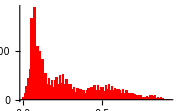

```mathematica
HM=Histogram[MonaF,{0.01},ChartStyle->Red]
```

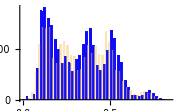

```mathematica
HMnew=Histogram[MonaNew1F,{0.01},ChartStyle->{Blue,Opacity[0.5]}]
```

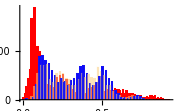

```mathematica
Show[HM,HMnew]
```

```mathematica
{MonaEq=HistogramTransform[Mona]}
```

{-Graphics-}

```mathematica
{MonaRE,MonaGE,MonaBE}=ColorSeparate[MonaEq]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{MonaR,MonaG,MonaB}=ColorSeparate[Mona]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{MonaGnew=HistogramTransform[MonaG]}
```

{-Graphics-}

```mathematica
a=1
```

1

```mathematica
f2[x_]:=x+x (1-x)*a
```

```mathematica
{MonaBnew=ImageApply[f2,MonaB]}
```

{-Graphics-}

```mathematica
{Monanew=ColorCombine[{MonaR,MonaGnew,MonaBnew}]}
```

{-Graphics-}

```mathematica
P1=Import["pill1.jpg"]
```

-Graphics-

```mathematica
P2=Import["pill2.jpg"]
```

-Graphics-

```mathematica
{PG1=ColorConvert[P1,"Grayscale"],PG2=ColorConvert[P2,"Grayscale"]}
```

{-Graphics-,-Graphics-}

```mathematica
DP1P2=ImageDifference[PG1,PG2]
```

-Graphics-

```mathematica
Result=ColorNegate[DP1P2]
```

-Graphics-

```mathematica
{Pirat1=Import["pirat.gif"]}
```

{-Graphics-}

```mathematica
{Pirat=RemoveAlphaChannel[Pirat1]}
```

{-Graphics-}

```mathematica
DimP=ImageDimensions[Pirat]
```

{300,180}

```mathematica
xPir=DimP[[1]]
```

300

```mathematica
yPir=DimP[[2]]
```

180

```mathematica
Pirat=ImagePartition[Pirat,{xPir /2,yPir}]
```

{{-Graphics-,-Graphics-}}

```mathematica
Part1=Pirat[[1]][[1]]
```

-Graphics-

```mathematica
Part2=Pirat[[1]][[2]]
```

-Graphics-

```mathematica
Part1G=ColorConvert[Part1,"Grayscale"]
```

-Graphics-

```mathematica
Part2G=ColorConvert[Part2,"Grayscale"]
```

-Graphics-

```mathematica
Diff=ImageDifference[Part1G,Part2G]
```

-Graphics-

```mathematica
DiffN=ColorNegate[Diff]
```

-Graphics-

```mathematica
{Part1,Part2,DiffN}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Bu=Import["bush.jpg"]}
```

{-Graphics-}

```mathematica
Ar:=Import["arnold.jpg"]
```

```mathematica
Morph[t_]:=Blend[{Bu,Ar},t]
```

```mathematica
Mor=Table[Morph[t],{t,0,1,0.01}];
```

```mathematica
{ListAnimate[Mor,AnimationRunning->False]}
```

{}